```mathematica
(*явный метод Эйлера на примере задачи о движении грузика*)
Clear["Global`*"]
```

```mathematica
{{Tabs = ReadList["C:\\Users\\anton\\source\\repos\\work1\\work1\\test.txt", {Number,Number(*, Number*)}];}, {□}}

(*Print[Tabs];*)
```

{{Null},{□}}

```mathematica
(*ListPointPlot3D[Tabs,PlotStyle->Blue,PlotStyle->Thin, PlotRange->All]*)
```

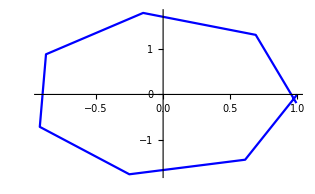

```mathematica
ListLinePlot[Tabs,PlotStyle->Blue, PlotStyle->Thin(*,PlotRange->{{-0.4,0.4} ,{-0.4,0.4}},AspectRatio->Automatic*)]
```

```mathematica
(*неявный метод Эйлера на примере задачи о движении грузика*)
```

```mathematica
(* (4*x^3+2*x^2-4*x+2)^(Sqrt[2])+ArcSin[1/(5+x-x^2) -5] *)
```

```mathematica
(*1/ArcTan[1+10*x^2]*)
(*1/(1+10*x^2)*)
```

```mathematica
(*Show[Plot[1/ArcTan[1+10*x^2],{x,-3,3},PlotRange->{0,1.5}, PlotStyle->Red],ListLinePlot[Tabs,PlotStyle->Blue]]*)
```

```mathematica
Tabs1 = ReadList["C:\\Users\\anton\\source\\repos\\work1\\work1\\test1.txt", {Number,Number}];
```

```mathematica
Tabs2 = ReadList["C:\\Users\\anton\\source\\repos\\work1\\work1\\test2.txt", {Number,Number}];
Tabs3 = ReadList["C:\\Users\\anton\\source\\repos\\work1\\work1\\test3.txt", {Number,Number}];
Tabs4 = ReadList["C:\\Users\\anton\\source\\repos\\work1\\work1\\test4.txt", {Number,Number}];
Tabs5 = ReadList["C:\\Users\\anton\\source\\repos\\work1\\work1\\test5.txt", {Number,Number}];
Tabs6 = ReadList["C:\\Users\\anton\\source\\repos\\work1\\work1\\test6.txt", {Number,Number}];
Tabs7 = ReadList["C:\\Users\\anton\\source\\repos\\work1\\work1\\test7.txt", {Number,Number}];
(*Tabs8 = ReadList["C:\\Users\\anton\\source\\repos\\work1\\work1\\test8.txt", {Number,Number}];*)
```

Show::gcomb: Could not combine the graphics objects in ….

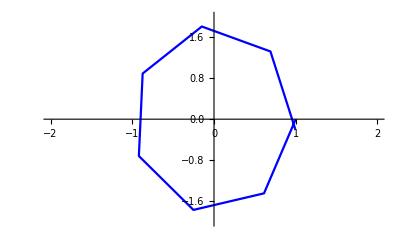
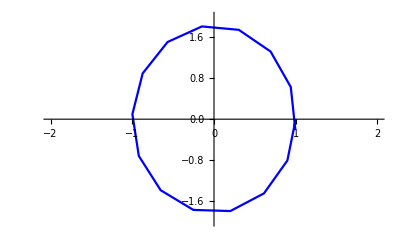
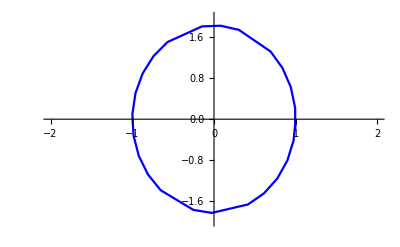
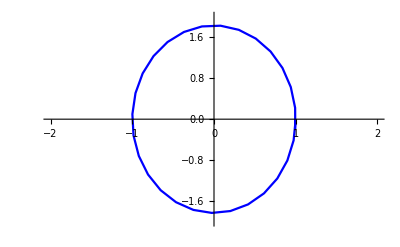
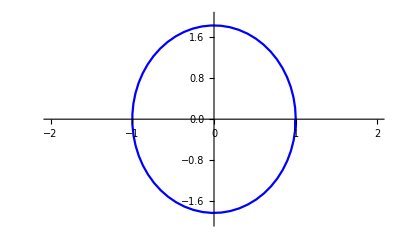
Show[-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,Lisc]

```mathematica
Show[ListLinePlot[Tabs1,PlotStyle->Blue, PlotStyle->Thin,PlotRange->{{-2,2} ,{-2,2}}],ListLinePlot[Tabs2,PlotStyle->Blue, PlotStyle->Thin,PlotRange->{{-2,2} ,{-2,2}}],
ListLinePlot[Tabs3,PlotStyle->Blue, PlotStyle->Thin,PlotRange->{{-2,2} ,{-2,2}}],
ListLinePlot[Tabs4,PlotStyle->Blue, PlotStyle->Thin,PlotRange->{{-2,2} ,{-2,2}}],
ListLinePlot[Tabs5,PlotStyle->Blue, PlotStyle->Thin,PlotRange->{{-2,2} ,{-2,2}}],
ListLinePlot[Tabs6,PlotStyle->Blue, PlotStyle->Thin,PlotRange->{{-2,2} ,{-2,2}}],Lisc(*,
ListLinePlot[Tabs8,PlotStyle->Pink,PlotStyle->Thin,PlotRange->{{-1,1},{-0,2}}]*)]
```

```mathematica
{{Tabstest = Import["C:\\Users\\anton\\source\\repos\\work1\\work1\\autostep1.txt","Table"];}, {□}}
```

{{Null},{□}}

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\anton\source\repos\work1\work1

```mathematica
autostep=Flatten@Import["autostep1.txt","Table"]
```

{0.03125,0.03125,0.03125,0.03125,0.03125,0.03125,0.03125,0.03125,0.03125,0.03125,0.03125,0.03125,0.03125,0.03125,0.03125,0.03125,0.03125,0.03125,0.0625,0.0625,0.0625,0.0625,0.03125,0.03125,0.03125,0.03125,0.0625,0.0625,0.0625,0.0625,0.03125,0.03125,0.03125,0.03125,0.03125,0.03125,0.03125,0.03125,0.03125,0.03125,0.03125,0.03125,0.03125,0.03125,0.03125,0.03125,0.03125,0.03125,0.03125,0.03125,0.03125,0.03125,0.03125,0.03125,0.03125,0.03125,0.03125,0.03125,0.03125,0.03125,0.03125,0.03125,0.03125,0.03125,0.03125,0.0625,0.0625,0.0625,0.0625,0.03125,0.03125,0.03125,0.03125,0.0625,0.0625,0.0625,0.0625,0.03125,0.03125,0.03125,0.03125,0.03125,0.03125,0.03125,0.03125,0.03125,0.03125,0.03125,0.03125,0.03125,0.03125,0.03125,0.03125,0.03125,0.03125,0.03125}

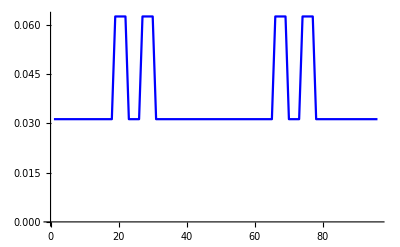

```mathematica
ListLinePlot[autostep, PlotStyle->Blue, PlotStyle->Thin]
```

```mathematica
autostepnew=Import["testnew.txt","Table"][[All,1]];
```

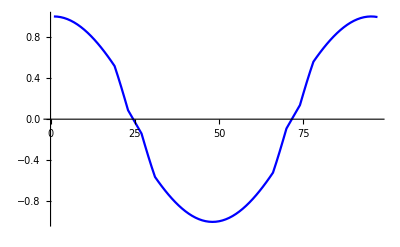

```mathematica
ListLinePlot[autostepnew, PlotStyle->Blue, PlotStyle->Thin]
```

```mathematica
delta=Import["delta.txt","Table"][[All,1]];
```

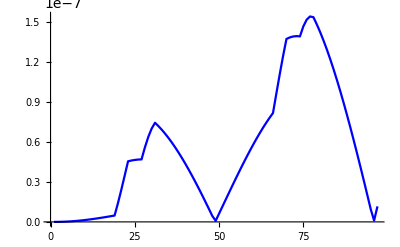

```mathematica
ListLinePlot[delta, PlotStyle->Blue, PlotStyle->Thin]
```